# Unit 2 - Functions and Their Graphs

Topics covered in this unit are listed below.

Defining a function

More on the evaluation of a function

Pure or anonymous functions

Defining piecewise-defined functions

Plotting a function of one variable

Drawing two functions with enclosed region shaded

Playing with Animate and Manipulate

## Defining a function

Functions can be defined in two ways, either by = (Set) or := (SetDelayed). We have seen the difference between = and := in assignment statement in Unit One. We’ll see more example in the aspect. Like with a variable, a function has a name consisting of English letters, digits, and/or $ (dollar sign). It must begin with an English letter or $.

```mathematica
f[x_]:=x^2-3x+2
g[x_]=x^2-3x+2;
h[x_,y_]:=Sqrt[x^2+y^2]
```

Two things must be clear.

[ ] must be used after the name of the function.

An underscore ( _ ) must follow each argument on the left hand side of = or :=. But on the right hand side, no underscore is used.

After a function is defined, it can be called the way as if it is built in Mathematica.

```mathematica
f[10]
```

72

```mathematica
g[10]
```

72

```mathematica
h[1,2]
```

√5

There is no difference between our f and g, though one is defined by = and the other by :=. But in certain cases, = and := produces different results.

```mathematica
k=1; (* value of variable k is set to 1 *)
f[x_]:=x^2-3x+k^2
g[x_]=x^2-3x+k^2;
k=2;(* new/present value of k is 2 now *)
```

```mathematica
f[0]
```

4

```mathematica
g[0]
```

1

In this example, f(x)=x^2-3x+4, but g(x)=x^2-3x+1. Why? Using := (SetDelayed), the definition of f(x) just records the formula x^2-3x+k, and the evaluation is delayed until the function is called. When we compute f(10), 10^2-3× 10+2^2 is evaluated, where 2 is the present value of k. But, with g(x), = (Set) is used and evaluation is done before the result is assigned to g(x). In other words, x^2-3x+1 is assigned to g(x).

In summary, when we define a function which depends on extra parameters, such as k in the example, beyond arguments of the function, we must be very careful in choosing = or :=. If the values of the parameters vary in time, = and := are different.

Another example involves the function Integrate.

```mathematica
f[x_]:=Integrate[x^2-3x+2,x] (* no output *)
g[x_]=Integrate[x^2-3x+2,x]
```

2 x-(3 x^2)/2+x^3/3

```mathematica
f[1]
```

Integrate::ilim: Invalid integration variable or limit(s) in 1.

∫0ⅆ1

```mathematica
g[1]
```

5/6

What is wrong with f(x)? Actually, f(x)=Integrate[x^2-3x+4,x], but g(x)=2 x-(3 x^2)/2+x^3/3. Why? Using :=, the definition of f(x) just records the formula Integrate[x^2-3x+2,x], and the evaluation is delayed until the function is called. When we compute f(1), Integrate[1^2-3×1+2,1]= Integrate[0,1] is evaluated, where the argument x is replaced with 1. But, with g(x), = is used and evaluation of Integrate[x^2-3x+2,x]is done before the result is assigned to g(x).

Similarly, you can understand the following example involving the function D (differentiation) or ∂_x .

```mathematica
f[x_]:=D[x^2-3x+2,x] (* no output *)
g[x_]=D[x^2-3x+2,x]
```

-3+2 x

```mathematica
f[1]
```

General::ivar: 1 is not a valid variable.

∂_1 0

```mathematica
g[1]
```

-1

## More on the evaluation of a function

There are three ways to evaluate a function at a point. The ordinary way is like f[x] and g[x,y] in algebra. The other two ways are valid when a function can accept one argument. They look like x//f or f@x. We have seen x//N many times. This postfix usage provides great convenience in many cases, especially when combined with the functions N or Simplify.

expr // f

```mathematica
Solve[x^2-3x+1==0,x]//N
```

{{x→0.381966},{x→2.61803}}

```mathematica
N[Solve[x^2-3x+1==0,x]]
```

{{x→0.381966},{x→2.61803}}

f@expr

```mathematica
N@π
```

3.14159

```mathematica
(Floor@2)*3.14
```

6.28

```mathematica
Floor@2*3.14
```

6.28

```mathematica
Floor@(2*3.14)
```

6

Floor@2*3.14 is actually (Floor@2)*3.14 or Floor[2]×3.14. And Floor@(2*3.14) is exactly Floor[2*3.14].

In practice, this prefix method is not used as much as the postfix form. However, if you don’t like [ ] embedded in too many other [ ]’s, it may help. For example,

```mathematica
Sqrt[Range[10]]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3,√10}

```mathematica
Length[Rest[Sqrt[Range[10]]]]
```

9

```mathematica
Length@Rest[Sqrt@Range@10]
```

9

## Pure or anonymous functions

Usually, when we need to evaluate the same expression multiple times, we define a function. However, in some cases, an expression is evaluated just once, but some values appear in the expression multiple times, such as 1.121^2-3×1.121+5×1.121×100 +100^2. We can certainly define a function for the expression like f[x_,y_]:=x^2-3x+5x*y+y^2 and then evaluate f[1.121,100]. It works. But if we do not want to introduce more symbols in our computation, we may use pure (or anonymous) function for the purpose.

With pure function, we define it this way: expression &. In the expression, #1 (or #), #2, #3, ⋯ represent the first, the second, the third, ⋯, arguments, respectively.

```mathematica
1.121^2-3 1.121+5 1.121 100+100^2
```

10558.4

```mathematica
f[x_,y_]:=x^2-3x+5x*y+y^2
f[1.121,100]
```

10558.4

```mathematica
#1^2-3#1+5#1*#2+#2^2&[1.121,100]
```

10558.4

```mathematica
(#1!)/(#2!(#1-#2)!)&[10,3]
```

120

Some built-in functions require a second function as one of its arguments. NestList is such an example. From the Wolfram Documentation, we can find the usage as follows.
“NestList[f,expr,n]: gives a list of the results of applying f to expr 0 through n times,” where a_1=expr is the first term, a_2=f(a_1) the second term, ⋯, a_(n+1)=f(a_n) the last term, of the list. In defining f(x) , we should know that x stands for the “previous” term and f(x) gives the present term.

```mathematica
f[x_]:=x+2
NestList[f,1,5]
```

{1,3,5,7,9,11}

```mathematica
NestList[#1+2&,1,5]  (* use anonymous function *)
```

{1,3,5,7,9,11}

## Defining piecewise-defined functions

The most frequently referred piecewise-defined function must be f(x)=∣x∣=Piecewise[{{x,, x≥0}, {-x,, x<0}}]. In the following examples, we define g(x)=Piecewise[{{x^2,, x<0}, {x,, 0≤x≤1}, {1-(x-1)^2,, x>1}}]. 

We can define a piecewise function by using one of the built-in functions, If, Which, and Piecewise.

If - Usage:

(1) If [condition, value]], if condition is true, return value; otherwise, do nothing.
           (2) If [condition, value_1, value_2], if condition is true, return value_1; otherwise, return value_2.

```mathematica
f[x_]:=If[x≥0,x,-x]
g[x_]:=If[x<0,x^2,If[x>1,1-(x-1)^2,x]]
```

Which - Usage: Which [condition_1,value_1,condition_2,value_2,⋯,condition_n,value_n], if condition_i is true for some i=1,2,⋯,n, return value_i.

```mathematica
f[x_]:=Which[x≥0,x,x<0,-x]
g[x_]:=Which[x<0,x^2,0≤x≤1,x,x>1,1-(x-1)^2]
```

Piecewise - Usage: Piecewise [{{value_1,condition_1},{value_2,condition_2},⋯,{value_n,condition_n}}]

```mathematica
f[x_]:=Piecewise[{{x,x≥0},{-x,x<0}}]
g[x_]:=Piecewise[{{x^2,x<0},{x,0≤x≤1},{1-(x-1)^2,x>1}}]
```

We can also input a piecewise-defined function by clicking the icon Piecewise[{{□, □}, {□, □}}] on a palette triggered by following the path, Palettes → Basic Math Assistant → Typesetting → ■^□, pressing Ctrl-⌤ to add a new row. You may also do it by pressing Esc pw Esc.

```mathematica
f[x_]:=Piecewise[{{x, x≥0}, {-x, x<0}}]
g[x_]:=Piecewise[{{x^2, x<0}, {x, 0≤x≤1}, {1-(x-1)^2, x>1}}]
```

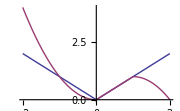

```mathematica
Plot[{f[x],g[x]},{x,-2,2},ImageSize->180]
```

Some built-in piecewise-defined functions

They include Abs, Ceiling, Floor, and Round. Their graphs are shown below. You may refer the Wolfram Documentation for more information.

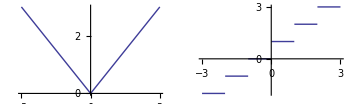

```mathematica
GraphicsRow[{Plot[Abs[x],{x,-3,3}],Plot[Ceiling[x],{x,-3,3}]},ImageSize->350]
```

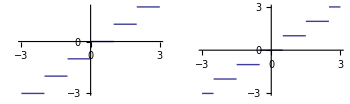

```mathematica
GraphicsRow[Table[Plot[f[x],{x,-3,3}],{f,{Floor, Round}}],ImageSize->350]
```

## Plotting a function of one variable

There are plenty of built-in Mathematica functions for plotting a function in 2-D and 3-D spaces. They are specifically designed for Cartesian (2-D and 3-D), polar (2-D), cylindrical (3-D), and spherical (3-D), coordinate systems. The polar coordinate system and the coordinate systems for 3-D space are introduced in Calculus II and III. We are now focusing on the function, Plot, for 2-D Cartesian coordinate system. It is the very basic tool.

Usage:

Plot[f,{x,x_min,x_max}], plotting f as a function of x from x_min to x_max.

Plot[{f_1,f_2,…},{x,x_min,x_max}], plotting a LIST of functions, f_1,f_2,….

Plot can take options so as to fine-tune the behavior or properties of the generated graph.

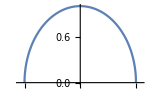

```mathematica
f[x_]:=Sqrt[1-x^2]
Plot[f[x],{x,-1.1,1.1},ImageSize->150]
(* plot the semicircle above the x-axis *)
```

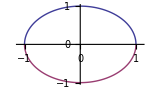

```mathematica
Plot[{f[x],-f[x]},{x,-1.1,1.1},ImageSize->150] 
(* draw a unit circle? it doesn't look like a circle *)
```

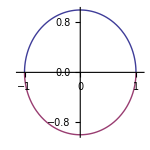

```mathematica
Plot[{f[x],-f[x]},{x,-1.1,1.1},AspectRatio->Automatic,ImageSize->150] 
(* now it looks like a circle *)
```

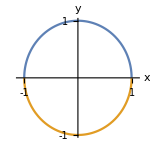

```mathematica
Clear[x,y]
Plot[{f[x],-f[x]},{x,-1.1,1.1},AspectRatio->Automatic,Ticks->{{-1,1},{-1,1}},AxesLabel->{x,y},ImageSize->150] 
(* simplify the graph by removing extra ticks, and add labels for axes *)
```

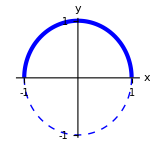

```mathematica
Clear[x,y]
Plot[{f[x],-f[x]},{x,-1.1,1.1},AspectRatio->Automatic,Ticks->{{-1,1},{-1,1}},AxesLabel->{x,y},PlotStyle->{{Blue,Thickness[.02]},{Blue,Thick, Dashed}},ImageSize->150] 
(* more games *)
```

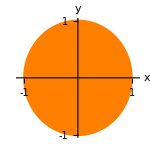

```mathematica
Clear[x,y]
Plot[{f[x],-f[x]},{x,-1.1,1.1},AspectRatio->Automatic,Ticks->{{-1,1},{-1,1}},AxesLabel->{x,y},PlotStyle->{Orange, Orange},Filling->{1->{2}},FillingStyle->Orange,ImageSize->150]
```

The option PlotRange can be very helpful especially when Plot cannot choose a proper range of a function by default.

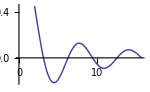

```mathematica
Plot[Sin[x]/x,{x,0,5Pi},ImageSize->150]
```

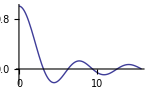

```mathematica
Plot[Sin[x]/x,{x,0,5Pi},PlotRange->All,ImageSize->150]
```

When plotting a function without specified interval, we need to choose one smartly. It should cover the subinterval in which we are interested. It had better cover both negative and positive numbers. We may start from a larger interval and, according to the resulting graphs, gradually narrow down to such a smaller interval that not much information is lost, and the graph looks balanced and beautiful if possible.

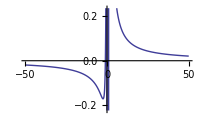

```mathematica
f[x_]:=(x+1)/(x(x-1))
Plot[f[x],{x,-50,50},ImageSize->200]
```

The graph does point to the fact that y=0 is the horizontal asymptote. But it loses too much details near x=0.

A few experiments with the interval lead to the following graph which doesn’t look much better but shows the existence of two vertical asymptotes.

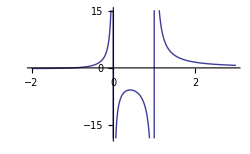

```mathematica
Plot[f[x],{x,-2,3}, ImageSize->250](*Plot[f[x],{x,-1.5,2}]*)
```

It is hard for us to tell from the graph if the curve is above or below the x-axis on the left end. We can use PlotRange to further fine tune the graph.

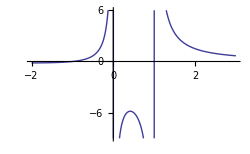

```mathematica
Plot[f[x],{x,-2,3},PlotRange->{-9,6},ImageSize->250]
```

The options Filling and FillingStyle can be used to shade regions on a graph.

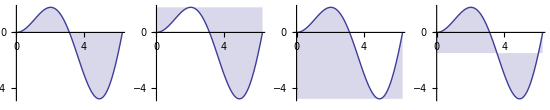

```mathematica
GraphicsRow[Table[Plot[x Sin[x],{x,0,2π},Filling->f],{f,{Axis, Top,Bottom,-1.5}}],ImageSize->550]
```

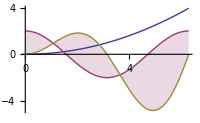

```mathematica
Plot[{ 1/10 x^2,2Cos[x],x Sin[x]},{x,0,2π},Filling->{2->{3}},ImageSize->200]
```

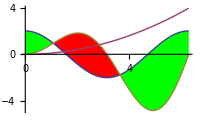

```mathematica
Plot[{ 2Cos[x],1/10 x^2,x Sin[x]},{x,0,2π},Filling->{1->{3}},FillingStyle->{Red,Green},ImageSize->200]
```

Think about how the color changes in this last graph. The next section will take advantage of the mechanism.

The built-in function Show

There are good reasons for Mathematica users to believe that Show is the best thing Mathematica can provide for plotting graphs. It combines multiple graphics like magical glue and shows the resultant graph. Usually, the first plot is also used to set up the canvas with basic settings such as image size and plot range, and Mathematica adds the next graphics to the canvas magically.

The next example plots two functions with a part of enclosed region shaded.

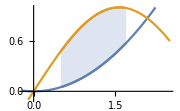

```mathematica
f[x_]:=1/5 x^2
g[x_]:=Sin[x]
Show[
Plot[{f[x],g[x]},{x,-0.2,2.5},PlotRange->{-0.1,1},ImageSize->180],(* the 1st plot must have the largest interval *)
Plot[{f[x],g[x]},{x,0.5,1.7},Filling->{1->{2}}]
]
```

Similarly, we can plot two functions with multiple parts of enclosed region shaded.

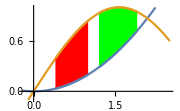

```mathematica
f[x_]:=1/5 x^2
g[x_]:=Sin[x]
Show[{
Plot[{f[x],g[x]},{x,-0.2,2.5},PlotRange->{-0.1,1},ImageSize->180],(* the 1st plot must have the largest interval *)
Plot[{f[x],g[x]},{x,0.4,1.0},Filling->{1->{2}},FillingStyle->Red],
Plot[{f[x],g[x]},{x,1.2,1.9},Filling->{1->{2}},FillingStyle->Green]
}]
```

## Drawing two functions with enclosed region shaded

In the following example, we draw the straight line y=1/2 x and the parabola y=(x-1)^2-3 with their enclosed region shaded.

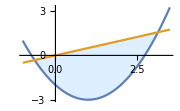

```mathematica
f[x_]:=(x-1)^2-3
g[x_]:=0.5x
Plot[{f[x],g[x]},{x,-1,3.5},Filling->{1->{2}},FillingStyle->{LightBlue,White},ImageSize->180]
(* "White" is used to cheat Mathematica. The background is White *)
```

The job can also be done as shown below, but it involves remarkably more work.

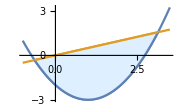

```mathematica
f[x_]:=(x-1)^2-3
g[x_]:=0.5x
(* find the x-coordinates of the two intersections *)
x1=x/.FindRoot[f[x]==g[x],{x,-4}];
x2=x/.FindRoot[f[x]==g[x],{x,3}];
Show[
Plot[{f[x],g[x]},{x,-1,3.5},ImageSize->180],
Plot[{f[x],g[x]},{x,x1,x2},Filling->{1->{2}},FillingStyle->LightBlue]
]
```

In addition, we can add labels to the graph as follows.

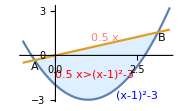

```mathematica
f[x_]:=(x-1)^2-3
g[x_]:=0.5x
Show[
Plot[{f[x],g[x]},{x,-1,3.5},Filling->{1->{2}},FillingStyle->{LightBlue,White},ImageSize->180],Graphics[Text[Style[g[x]>f[x],Red],{1.2,-1.3}]],
Graphics[Text[Style[f[x],Blue],{2.5,-2.7}]],
Graphics[Text[Style[g[x],Pink],{1.5,1.2}]],
Graphics[Text["A",{-0.64,-0.78}]],
Graphics[Text["B",{3.25,1.20}]]
]
```

In the next example, we draw two circles, x^2+y^2=4 and (x-2)^2+y^2=1, with the enclosed region inside both shaded.

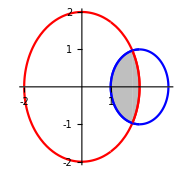

```mathematica
f[x_]:=Sqrt[4-x^2]
g[x_]:=Sqrt[1-(x-2)^2]
x0=x/.NSolve[f[x]==g[x],x][[1]];
Show[
Plot[{f[x],-f[x],g[x],-g[x]},{x,-2.05,3.05},AspectRatio->Automatic,PlotStyle->{Red,Red,Blue,Blue},Ticks->{{-2,-1,1,2},{-2,-1,1,2}},ImageSize->180],Plot[{f[x],-f[x],g[x],-g[x]},{x,x0,2},AspectRatio->Automatic,PlotStyle->{Red,Red,Blue,Blue},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Gray]],Plot[{g[x],-g[x]},{x,1,x0},AspectRatio->Automatic,PlotStyle->{Blue,Blue},Filling->{{1->{2}}},FillingStyle->Directive[Opacity[0.5],Gray]]
]
```

## Playing with Animate and Manipulate

When teaching and studying properties of functions, graphs are of great help, and animations are even greater tools. It is unbelievably simple to make animations with Mathematica.

The two built-in functions we are to use are Animate and Manipulate. Their usages are exactly the same to most people. You can easily tell they work differently and are good for different purposes. Have fun!

Usage:

Animate[expr,{u,u_min,u_max}],generating an animation of expr in which the parameter u varies continuously from u_min to u_max.

Animate[expr,{u,u_min,u_max,di}],generating an animation of expr in which the parameter u varies continuously from u_min to u_max with step di.

Animate[expr,{u,…},{v,…},…], letting multiple parameters u, v, … vary.

Animate and Manipulate pretend to have u change “continuously”. Therefore, Animate[expr,{u,u_min,u_max}] is NOTE Animate[expr,{u,u_min,u_max,1}]. In other words, if step is 1, we must specify.

```mathematica
Animate[Plot[Sin[k x],{x,-Pi,Pi},ImageSize->160],{k,1,10,2},Alignment->Center]
```

```mathematica
Animate[Plot[c Sin[k x+b],{x,-Pi,Pi},PlotRange->{-10,10},ImageSize->160],{{c,6} ,{1, 3, 6,9, 10}},{k,1,10},{b,-2,2,0.2},AnimationRunning->False,Alignment->Center]
```

```mathematica
Manipulate[Plot[Sin[k x],{x,-Pi,Pi},ImageSize->160],{k,1,10,2},Alignment->Center]
```

```mathematica
Manipulate[Plot[c Sin[k x+b],{x,-Pi,Pi},PlotRange->{-10,10},ImageSize->160],{{c,3} ,{1, 3, 9, 10}},{k,1,10,Appearance->"Open"},{b,-2,2,0.2},Alignment->Center]
```

The next example shows problems you will possibly face soon.

```mathematica
f[x_]:=Sin[x]
Animate[Plot[ f[k*x],{x,-Pi,Pi},ImageSize->160],{k,0,10},Alignment->Center]
```

Now, you move on to next problem and will define f(x) for your new needs.

```mathematica
f[x_]:=x^2
```

After you input and run this code, what will happen to the previous animation? It animates this new function automatically!

To prevent this from happening, we had better do animation in the following way by using Module and making f local. (See Unit 4 for more information about Module.)

```mathematica
Animate[Module[{f},(* this local f makes global f invisible *)
f[x_]:=Sin[x];Plot[ f[k*x],{x,-Pi,Pi},ImageSize->160]],{k,0,10},Alignment->Center]
```

Except Animate with option AnimationRunning→False, Animate and Manipulate are always alive, by which we mean, after writing and executing the code the first time, they are always running whenever you reopen the hosting notebook, without the need to manually execute the code again. Of course, they disappear when you remove their code or output. The problem is Mathematica seeks to run just the Animate and Manipulate commands in a notebook. Therefore, an animation fails to work if it depends on user-defined functions and/or variables defined outside the very Animate or Manipulate command. Therefore, it is strongly recommended that an Animate or Manipulate command only access Mathematica built-in symbols; if other information is needed, have it combined into the Animate or Manipulate command.

Compare what you will see of these last two animations by exiting and restarting Mathematica and, then, reopening this very notebook.

```mathematica
f[x_]:=Sin[x];
Animate[Plot[ f[k*x],{x,-Pi,Pi},ImageSize->160],{k,0,10}]
```

It does not work because the Animate command depends on the “external” user-defined function f(x). But the following code works because the user-defined function f(x) is inside and, thus, part of, the Animate command.

```mathematica
Animate[Module[{f},f[x_]:=Sin[x];Plot[ f[k*x],{x,-Pi,Pi},ImageSize->160]],{k,0,10}]
```

Then, how about the following code?

```mathematica
Module[{f},
f[x_]:=Sin[x];
Animate[Plot[ f[k*x],{x,-Pi,Pi},ImageSize->160],{k,0,10}]]
```

It doesn’t work either because, again, Mathematica automatically runs the very Animate and Manipulate commands only. This is really weird. We wish it take this last code in its new versions.

© 2015-2023 by David Wang, dwang@liberty.edu